## Chapter II A Sample Project in Mathematica

### Question: what part of the world has the highest life expectancy? Wolfram Knowledgebase data

WolframAlphaQueryResults(*Free-form input is useful for looking up data or performing initial calculations because you can start using it immediately without knowing anything about the underlying syntax or structure of the Wolfram Language.*)

-Graphics-(from 1950 to 2020)
(in years)

```mathematica
CountryData["China","LifeExpectancy"]
```

77.097 yr

```mathematica
data=DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData[All]}],{_,_Missing}];
```

```mathematica
TableForm[%72]
```

Afghanistan | 65.173 yr
Albania | 78.686 yr
Algeria | 77.063 yr
American Samoa | 73.9 yr
Andorra | 82.9 yr
Angola | 61.487 yr
Anguilla | 81.6 yr
Antigua and Barbuda | 77.146 yr
Argentina | 76.813 yr
Armenia | 75.224 yr
Aruba | 76.434 yr
Australia | 83.586 yr
Austria | 81.671 yr
Azerbaijan | 73.123 yr
Bahamas | 74.053 yr
Bahrain | 77.419 yr
Bangladesh | 72.868 yr
Barbados | 79.308 yr
Belarus | 74.951 yr
Belgium | 81.786 yr
Belize | 74.754 yr
Benin | 62.077 yr
Bermuda | 81.5 yr
Bhutan | 72.08 yr
Bolivia | 71.771 yr
Bosnia and Herzegovina | 77.545 yr
Botswana | 69.793 yr
Brazil | 76.084 yr
British Virgin Islands | 78.9 yr
Brunei | 75.998 yr
Bulgaria | 75.168 yr
Burkina Faso | 61.981 yr
Burundi | 61.916 yr
Cambodia | 70.054 yr
Cameroon | 59.626 yr
Canada | 82.569 yr
Cape Verde | 73.166 yr
Cayman Islands | 81.4 yr
Central African Republic | 53.679 yr
Chad | 54.505 yr
Chile | 80.329 yr
China | 77.097 yr
Colombia | 77.46 yr
Comoros | 64.525 yr
Cook Islands | 76.2 yr
Costa Rica | 80.465 yr
Croatia | 78.638 yr
Cuba | 78.892 yr
Curacao | 79.029 yr
Cyprus | 81.135 yr
Czech Republic | 79.521 yr
Democratic Republic of the Congo | 60.971 yr
Denmark | 81.027 yr
Djibouti | 67.49 yr
Dominica | 77.4 yr
Dominican Republic | 74.257 yr
East Timor | 69.712 yr
Ecuador | 77.216 yr
Egypt | 72.15 yr
El Salvador | 73.533 yr
Equatorial Guinea | 59.057 yr
Eritrea | 66.679 yr
Estonia | 78.897 yr
Ethiopia | 66.953 yr
Falkland Islands | 77.9 yr
Faroe Islands | 80.6 yr
Fiji | 67.561 yr
Finland | 82.077 yr
France | 82.784 yr
French Guiana | 80.093 yr
French Polynesia | 77.836 yr
Gabon | 66.69 yr
Gambia | 62.383 yr
Gaza Strip | 74.4 yr
Georgia | 73.919 yr
Germany | 81.478 yr
Ghana | 64.347 yr
Gibraltar | 79.7 yr
Greece | 82.405 yr
Greenland | 72.9 yr
Grenada | 72.426 yr
Guadeloupe | 82.328 yr
Guam | 80.277 yr
Guatemala | 74.529 yr
Guernsey | 82.7 yr
Guinea | 61.962 yr
Guinea-Bissau | 58.634 yr
Guyana | 70.023 yr
Haiti | 64.315 yr
Honduras | 75.448 yr
Hong Kong | 85.003 yr
Hungary | 77.026 yr
Iceland | 83.138 yr
India | 69.887 yr
Indonesia | 71.908 yr
Iran | 76.87 yr
Iraq | 70.748 yr
Ireland | 82.479 yr
Isle of Man | 81.4 yr
Israel | 83.123 yr
Italy | 83.663 yr
Ivory Coast | 58.104 yr
Jamaica | 74.586 yr
Japan | 84.766 yr
Jersey | 82. yr
Jordan | 74.655 yr
Kazakhstan | 73.824 yr
Kenya | 66.991 yr
Kiribati | 68.611 yr
Kosovo | 71.6463 yr
Kuwait | 75.586 yr
Kyrgyzstan | 71.587 yr
Laos | 68.219 yr
Latvia | 75.415 yr
Lebanon | 79.004 yr
Lesotho | 54.836 yr
Liberia | 64.423 yr
Libya | 73.082 yr
Liechtenstein | 82. yr
Lithuania | 76.1 yr
Luxembourg | 82.401 yr
Macau | 84.37 yr
North Macedonia | 75.918 yr
Madagascar | 67.39 yr
Malawi | 64.694 yr
Malaysia | 76.306 yr
Maldives | 79.208 yr
Mali | 59.692 yr
Malta | 82.682 yr
Marshall Islands | 73.6 yr
Martinique | 82.723 yr
Mauritania | 65.129 yr
Mauritius | 75.13 yr
Mayotte | 79.526 yr
Mexico | 75.131 yr
Micronesia | 68.002 yr
Moldova | 72.006 yr
Monaco | 89.4 yr
Mongolia | 70.056 yr
Montenegro | 77.014 yr
Montserrat | 74.8 yr
Morocco | 76.901 yr
Mozambique | 61.387 yr
Myanmar | 67.363 yr
Namibia | 64.045 yr
Nauru | 67.8 yr
Nepal | 71.067 yr
Netherlands | 82.424 yr
New Caledonia | 77.726 yr
New Zealand | 82.434 yr
Nicaragua | 74.697 yr
Niger | 62.792 yr
Nigeria | 55.018 yr
Northern Mariana Islands | 75.6 yr
North Korea | 72.453 yr
Norway | 82.546 yr
Oman | 78.078 yr
Pakistan | 67.428 yr
Palau | 73.6 yr
Panama | 78.68 yr
Papua New Guinea | 64.725 yr
Paraguay | 74.363 yr
Peru | 76.947 yr
Philippines | 71.36 yr
Poland | 78.901 yr
Portugal | 82.233 yr
Puerto Rico | 80.265 yr
Qatar | 80.363 yr
Republic of the Congo | 64.804 yr
Réunion | 80.758 yr
Romania | 76.183 yr
Russia | 72.742 yr
Rwanda | 69.329 yr
Saint Helena, Ascension and Tristan da Cunha | 79.8 yr
Saint Kitts and Nevis | 76.2 yr
Saint Lucia | 76.343 yr
Saint Martin | 79.622 yr
Saint Pierre and Miquelon | 80.7 yr
Saint Vincent and the Grenadines | 72.658 yr
Samoa | 73.45 yr
San Marino | 83.4 yr
São Tomé and Príncipe | 70.583 yr
Saudi Arabia | 75.28 yr
Senegal | 68.213 yr
Serbia | 76.144 yr
Seychelles | 73.483 yr
Sierra Leone | 55.066 yr
Singapore | 83.767 yr
Sint Maarten | 78.5 yr
Slovakia | 77.685 yr
Slovenia | 81.475 yr
Solomon Islands | 73.132 yr
Somalia | 57.697 yr
South Africa | 64.379 yr
South Korea | 83.193 yr
South Sudan | 58.095 yr
Spain | 83.693 yr
Sri Lanka | 77.144 yr
Sudan | 65.53 yr
Suriname | 71.802 yr
Eswatini | 60.721 yr
Sweden | 82.946 yr
Switzerland | 83.921 yr
Syria | 73.651 yr
Taiwan | 80.626 yr
Tajikistan | 71.301 yr
Tanzania | 65.815 yr
Thailand | 77.344 yr
Togo | 61.34 yr
Tonga | 71.018 yr
Trinidad and Tobago | 73.628 yr
Tunisia | 76.891 yr
Turkey | 77.928 yr
Turkmenistan | 68.313 yr
Turks and Caicos Islands | 80.1 yr
Tuvalu | 67.2 yr
Uganda | 63.713 yr
Ukraine | 72.184 yr
United Arab Emirates | 78.12 yr
United Kingdom | 81.426 yr
United States | 78.9 yr
United States Virgin Islands | 80.747 yr
Uruguay | 78.056 yr
Uzbekistan | 71.848 yr
Vanuatu | 70.623 yr
Venezuela | 72.066 yr
Vietnam | 75.493 yr
Wallis and Futuna Islands | 80. yr
West Bank | 75.4 yr
Western Sahara | 70.505 yr
Yemen | 66.181 yr
Zambia | 64.194 yr
Zimbabwe | 61.738 yr

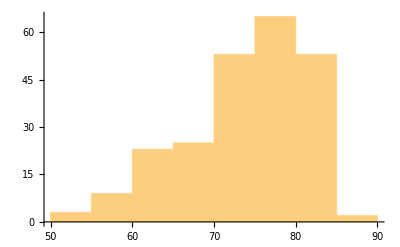

```mathematica
Histogram[data[[All,2]]]
```

```mathematica
dataAfrica=DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Africa"]}],{_,_Missing}];
Mean[dataAfrica[[All,2]]]
```

65.3263 yr

```mathematica
dataAsia=DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Asia"]}],{_,_Missing}];
Mean[dataAsia[[All,2]]]
```

74.7317 yr

```mathematica
dataEurope=DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Europe"]}],{_,_Missing}];
Mean[dataEurope[[All,2]]]
```

80.0636 yr

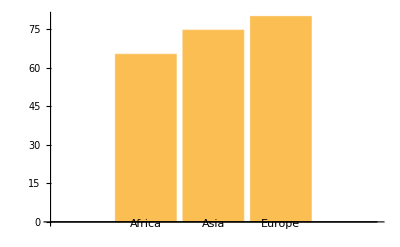

```mathematica
BarChart[{Mean[dataAfrica[[All,2]]],Mean[dataAsia[[All,2]]],Mean[dataEurope[[All,2]]]},ChartLabels->{"Africa","Asia","Europe"}]
```

```mathematica
dataSouthAmerica=DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["SouthAmerica"]}],{_,_Missing}];
Take[dataSouthAmerica,3]
```

{{Argentina,76.813 yr},{Bolivia,71.771 yr},{Brazil,76.084 yr}}

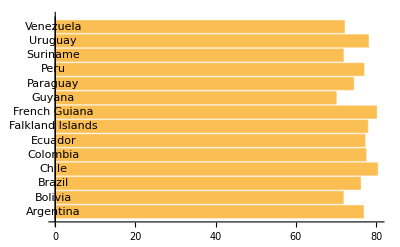

```mathematica
BarChart[dataSouthAmerica[[All,2]],ChartLabels->dataSouthAmerica[[All,1]],BarOrigin->Left]
```

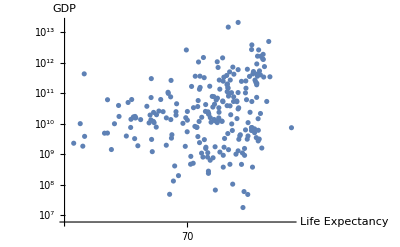

```mathematica
data=Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"GDP"]},CountryData[i,"Name"]],{i,CountryData[]}];
ListLogLogPlot[data,AxesLabel->{"Life Expectancy","GDP"}]
```

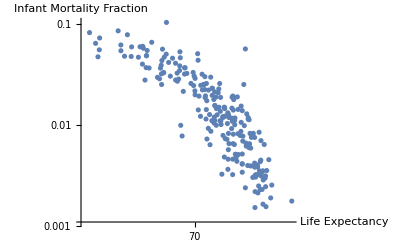

```mathematica
data=Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,"InfantMortalityFraction"]},CountryData[i,"Name"]],{i,CountryData[]}];
ListLogLogPlot[data,AxesLabel->{"Life Expectancy","Infant Mortality Fraction"}]
```

```mathematica
Manipulate[plotFn[Table[Tooltip[{CountryData[i,"LifeExpectancy"],CountryData[i,prop]},CountryData[i,"Name"]],{i,CountryData[All]}],AxesLabel->{"Life Expectancy",prop}],{prop,{"GDP","InfantMortalityFraction","LiteracyFraction"}},{{plotFn,ListLogLogPlot},{ListPlot,ListLogPlot,ListLogLogPlot}},SaveDefinitions->True]
```

```mathematica
Clear[data,dataAfrica,dataAsia,dataEurope,dataSouthAmerica]
```